```mathematica
sol = DSolve[{p1'[t]==4*x1[t]^3,p2'[t]==4*x2[t]^3,x1'[t]==-4*p1[t]^3, x2'[t]==-4*p2[t]^3,x1[0]==2.,x2[0]==1.,p1[0]==0.,p2[0]==0.},{p1,p2,x1,x2},t]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

General::stop: Further output of DSolve::bvnul will be suppressed during this calculation.

{{x1→Function[{t},(16.-(InverseFunction[(Hypergeometric2F1[1/4,3/4,5/4,#1^4/(4 4.)] #1 (1-#1^4/(4 4.))^(3/4))/((4 4.-#1^4)^(3/4))&][4 t])^4)^(1/4)],p1→Function[{t},InverseFunction[(Hypergeometric2F1[1/4,3/4,5/4,#1^4/(4 4.)] #1 (1-#1^4/(4 4.))^(3/4))/((4 4.-#1^4)^(3/4))&][4 t]],x2→Function[{t},(1.-(InverseFunction[(Hypergeometric2F1[1/4,3/4,5/4,#1^4/(4 0.25)] #1 (1-#1^4/(4 0.25))^(3/4))/((4 0.25-#1^4)^(3/4))&][4 t])^4)^(1/4)],p2→Function[{t},InverseFunction[(Hypergeometric2F1[1/4,3/4,5/4,#1^4/(4 0.25)] #1 (1-#1^4/(4 0.25))^(3/4))/((4 0.25-#1^4)^(3/4))&][4 t]]}}

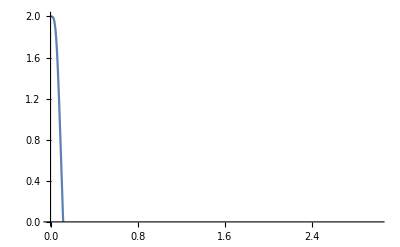

```mathematica
Plot[{x1[t]/.sol},{t,0,3}]
```